Math 272: Google's PageRank Algorithm

Names: 

	Please email your completed file to npflueger@amherst.edu by Wednesday night.

### Eigenvalues and Eigenvectors in Mathematica

To find the eigenvalues and corresponding eigenvectors of a matrix in Mathematica, you can use the Eigensystem command. For example, we find the eigenvalues and eigenvectors of the matrix (0 | 1
1 | 0) as follows:

```mathematica
A = {{0,1},{1,0}};
Eigensystem[A]//MatrixForm
```

(-1 | 1
{-1,1} | {1,1})

Note that it is often convenient to print the result in decimal form, especially for larger matrices. To do this, add the command “ // N “ before MatrixForm, as below. In this case it doesn’t make much difference; it merely means a decimal point is printed after each 1.

```mathematica
Eigensystem[A] // N // MatrixForm
```

(-1. | 1.
{-1.,1.} | {1.,1.})

The output informs us that this matrix reflects (-1
1) through the origin (multiplies it by -1) and fixes the vector (1
1) in place. This matrix represents a reflection through the axis y=x (which is spanned by (1
1)).

Exercise 1. Consider the matrix (5/13 | 12/13
12/13 | -5/13). As a linear tranformation, it is also a reflection. Using the Eigensystem command, determine the axis of reflection.

Note that the Eigensystem command will sometimes give complex numbers in its output. You do not need to worry too much about the meaning of these today, but you may see them in the output. For example, you might see things like the following.

```mathematica
A = {{4/5,-3/5},{3/5,4/5}};
A // MatrixForm
Eigensystem[A]// N // MatrixForm
```

(4/5 | -3/5
3/5 | 4/5)

(0.8+0.6 ⅈ | 0.8-0.6 ⅈ
{0.+1. ⅈ,1.} | {0.-1. ⅈ,1.})

### The PageRank algorithm: basic idea

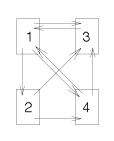
The remaining exercises are taken from the article “The 25 Billion Dollar Eigenvector,” by Kurt Bryan and Tanya Leise (our department chair), available on the website. They explore some aspects of an algorithm called PageRank (named for Larry Page, one of the founders of Google), which is the original algorithm used by Google to order its search results. Today, PageRank is one of many algorithms used for this purpose by Google, but PageRank remains the most famous, partly because of its surprising simplicity and effectiveness.

The PageRank algorithm begins by modeling the web as a network like the one shown below. Each node is a webpage, and each arrow is a link from one webpage to another.
Figure 1.  -Graphics-
From this web, one constructs a link matrix, as follows. Entry i,j in the matrix is equal to the proportion of the links out of page j that are directed to page i. For example, the link matrix of the network in Figure 1 is as follows.

```mathematica
A={{0,0,1,1/2},{1/3,0,0,0},{1/3,1/2,0,1/2},{1/3,1/2,0,0}};A//MatrixForm
```

(0 | 0 | 1 | 1/2
1/3 | 0 | 0 | 0
1/3 | 1/2 | 0 | 1/2
1/3 | 1/2 | 0 | 0)

The basic idea of PageRank is this: we look for an eigenvector with eigenvalue 1, and use its coordinates as “scores” to rank the pages in the network (see section 2.1 of the Bryan-Leise article for a discussion of why this is a good way to score the pages).

```mathematica
Eigensystem[A]//N // MatrixForm
```

(1. | -0.360623+0.410976 ⅈ | -0.360623-0.410976 ⅈ | -0.278753
{2.,0.666667,1.5,1.} | {-2.02681-0.403759 ⅈ,0.629961+1.09112 ⅈ,0.39685-0.687365 ⅈ,1.} | {-2.02681+0.403759 ⅈ,0.629961-1.09112 ⅈ,0.39685+0.687365 ⅈ,1.} | {1.05362,-1.25992,-0.793701,1.})

In this example, the first column tells us an eigenvector with eigenvalue 1 (don’t worry about the complex eigenvalues in the other columns). We can extract these “scores” directly as follows.

```mathematica
v=Eigensystem[A][[2,1]](* grabs eigenvector with eigenvalue 1, that is in the 2nd row, 1st column *)
```

{2,2/3,3/2,1}

Finally, it is conventional to “normalize” the scores so that they sum to 1. You can do this concisely using the following syntax (the expression Norm(v,1) gives the sum of the absolute values of the coordinates of v).

```mathematica
u=v/Norm[v,1] (* divides vector by the sum of its components, indexed 1 through 4, so that vector u's components will sum to 1 *)
```

{12/31,4/31,9/31,6/31}

Based on the vector u, page 1 has the highest ranking, followed by page 3, then page 4, then page 2.

### Shortcomings of the basic PageRank algorithm

There are some shortcomings of the basic system described above. One is that it is possible to “game the rankings,” as in the following exercise.

Exercise 2 (Exercise 1 in Bryan-Leise). Suppose the people who own page 3 in the web of Figure 1 are infuriated by the fact that its importance score, computed using formula (1), is lower than the score of page 1. In an attempt to boost page 3’s score, they create a page 5  that links to page 3; page 3 also links to page 5. Does this boost page 3’s score above that of page 1?

Exercise 3. Consider the network in Figure 2 below. Find the Eigensystem of the link matrix, and observe that “1” occurs more than once as an eigenvalue. This means that the space of eigenvectors for λ = 1 is more than 1-dimensional (the dimension is the number of times the eigenvalue occurs in the output of Eigensystem). Explain the meaning of the two eigenvectors that Mathematica produces, in terms of ranking of the five webpages.

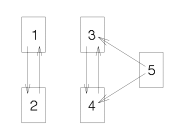
Figure 2.  -Graphics-

Exercise 4 (Exercise 3 in Bryan-Leise). Add a link from page 5 to page 1 in the web of Figure 2. The resulting web (considered as an “undirected graph”), is connected.  What is the dimension of the eigenspace for eigenvalue 1?

Note: A second shortcoming of the “basic PageRank” system is that it does not behave well when there are pages that do not link to any other pages (referred to as “dangling nodes” in Bryan-Leise). I encourage you to experiment to see why these are problematic, and think about possible solutions, but we will not go into this issue in the lab.

### A remedy to the “multiple eigenvectors” issue

The problem illustrated in Exercise 3 results from the fact that there the network breaks into pieces that don’t link to each other. There is a slick way to fix this issue: rather than using the original “link matrix” A, consider a new matrix M, obtained as follows: choose a number m (between 0 and 1), multiply all entries of A by (1-m), and then add m/n to all entries.

To find M in Mathematica, you can say M=(1-m)A+m/n.  That will add m/n to every entry of the matrix.

When Google was launched in the late 90’s, Page and Brin chose the value m = 0.15. Here’s a nice way to interpret the matrix M in this case: imagine a new web, where 15% of all the links for any given page are equally distributed among all the pages in the entire network, while the remaining 85% of the links are distributed according to the links in the original web. This new web is very well-connected, which turns out to remedy the problem in Exercise 3.

Exercise 5 (Exercise 11 in Bryan-Leise). Consider again the web in Figure 1, with the addition of a page 5 that links to page 3, where page 3 also links to page 5. Calculate the new ranking by finding the eigenvector of M (corresponding to λ = 1) that has positive components summing to 1. Use m = 0.15.

Exercise 6 (Exercise 12 in Bryan-Leise). Add a sixth page that links to every page of the web in the previous exercise, but to which no other page links. Rank the pages using A, then using M with m = 0.15, and compare the results..00M 
k 
x0 
−q.001 and 
.00M 
k 
x0 
−q.001 
.00M 
k 
−1 x0 
−q.001 for k = 1, 5, 10, 50 using an initial guess x0 not too close to the actual 
eigenvector q (so that you can watch the convergence). Determine c = max1 
≤j n 1 2 minM| and the absolute value of the second-largest eigenvalue of

Exercise 7 (based on Exercise 13 in Bryan-Leise). Determine the ranking of the pages in the web of Figure 2 given by M with m = 0.15..00M 
k 
x0 
−q.001 and 
.00M 
k 
x0 
−q.001 
.00M 
k 
−1 x0 
−q.001 for k = 1, 5, 10, 50 using an initial guess x0 not too close to the actual 
eigenvector q (so that you can watch the convergence). Determine c = max1 
≤j n 1 2 minM| and the absolute value of the second-largest eigenvalue of